## Problema 2

## a)

Escolha de seed e resolução das equações diferenciais

```mathematica
SeedRandom[90373];
nmass =20;
tmax = 2^(15);
newteqns=Table[u[k]''[t] ==If[k==1,-(u[k][t]-u[k+1][t]),If[k==nmass,-(u[k][t]-u[k-1][t]),-(2u[k][t]-u[k+1][t]-u[k-1][t])]],{k,1,nmass}];
funcs=Table[u[k][t],{k,1,nmass}];
initpos=Table[u[k][0]==0.2*RandomReal[{-0.5,0.5}],{k,1,nmass}];
initvel=Table[u[k]'[0]==0,{k,1,nmass}];
eqns = Join[newteqns,initpos,initvel];
sols=NDSolve[eqns,funcs,{t,0,tmax}];0;
```

```mathematica
dt = 1/2;
sampledSols =Table[First[u[i][t]/.sols],{i,1,20},{t,dt,tmax,dt}];0;
```

Trajetória das 3 primeiras massas

```mathematica
(*sampledSols2 = Table[First[u[i][t]/.sols],{i,1,20},{t,0.01,2,0.01}];*)
```

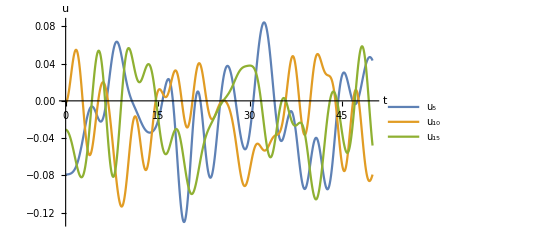

```mathematica
Plot[{u[1][t]/.sols,u[10][t]/.sols,u[20][t]/.sols},{t,0,50},AxesLabel->Evaluate[Style[#,Larger]&/@{"t","u"}],PlotLegends->{"u_5","u_10","u_15"}]
```

## b)

```mathematica
dOmega =N@ 2 Pi/tmax
```

0.000191748

Transformadad de Fourier Discreta da trajetórias das massas

```mathematica
FFT = Fourier/@sampledSols;
FFTpoints =Transpose[{dOmega Range[-(tmax/(2*dt)),(tmax/(2*dt))-1],#}]&/@Join[FFT[[All,(tmax/(2*dt))+1;;tmax/dt]],FFT[[All,1;;(tmax/(2*dt))]],2];
```

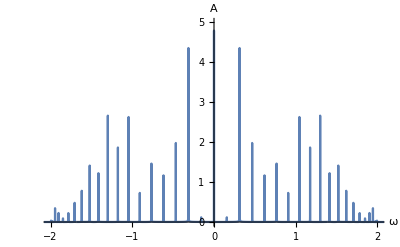

```mathematica
ListLinePlot[MapAt[Abs,FFTpoints[[1]] ,{All,2}  ],PlotRange->{{-2,2},{0,5}},AxesLabel->Evaluate[Style[#,Larger]&/@{"ω","A"}] ]
```

```mathematica
omegaList = {805,1620,2432,3218,3982,4733,5446,6182,6772,7366,7927,8422,8892,9285,9626,9906,10134,10290,10386};
peakWidth=50;
```

Identificação das frequências

```mathematica
omegaMaxList =( N[# 2Pi/tmax])&/@Total[{omegaList-peakWidth, (First@Ordering[#,-1]-2)&/@Table[FFT[[i,omegaList[[i]]-peakWidth;;omegaList[[i]]+peakWidth ]],{i,1,19}] }]
```

{0.15685,0.31274,0.466714,0.618003,0.765265,0.908117,1.04483,1.19478,1.29871,1.41414,1.52094,1.61816,1.7054,1.78191,1.84768,1.90194,1.9449,1.97519,1.99379}

## c)

```mathematica
selectPeak[omega_,width_]:=Module[{peak},
peak = FFT;
peak[[All,;;omega-width-1]]=0;
peak[[All,omega+width+1;;-omega-width]]=0;
peak[[All,-omega+width+2;;]]=0;
peak
];
```

Seleção do terceiro pico

```mathematica
omegaList
```

{805,1620,2432,3218,3982,4733,5446,6182,6772,7366,7927,8422,8892,9285,9626,9906,10134,10290,10386}

```mathematica
omegaMaxIndexList =Total[{omegaList-peakWidth, (First@Ordering[#,-1]-2)&/@Table[FFT[[i,omegaList[[i]]-peakWidth;;omegaList[[i]]+peakWidth ]],{i,1,19}] }]
```

{818,1631,2434,3223,3991,4736,5449,6231,6773,7375,7932,8439,8894,9293,9636,9919,10143,10301,10398}

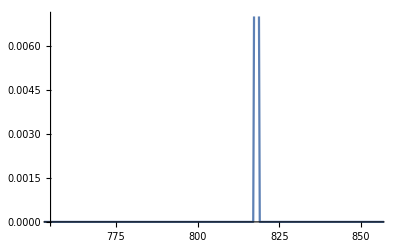

```mathematica
peaks =selectPeak[#,0]&/@omegaMaxIndexList;0;
ListLinePlot[Abs/@peaks[[1,3]],PlotRange->{{omegaList[[1]]-50,omegaList[[1]]+50},{0,0.007}}]
```

```mathematica
harmonics =Chop@ Map[InverseFourier,peaks,{2}];
```

```mathematica
ListLinePlot[harmonics[[3]],PlotRange->{{500,550},{-0.001,0.001}},AxesLabel->{"2 t","u_i"}]
```

-Graphics-

```mathematica
maxIndex =First@Ordering[#,-1]&/@harmonics[[All,1,500;;800]]
```

{129,151,283,18,285,18,7,59,130,228,169,187,244,282,207,116,292,125,159}

```mathematica
harmonicsFreeze =Table[ harmonics[[i,j,maxIndex[[i]] +500-1]], {i,1,19},{j,1,20}];
```

Terceiro modo normal

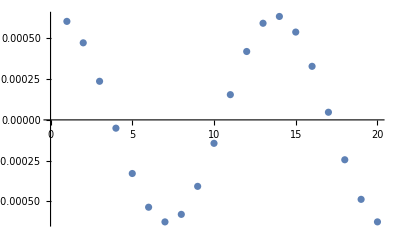

```mathematica
ListPlot[harmonicsFreeze[[3]]]
```

```mathematica
envTable3 =NonlinearModelFit[harmonicsFreeze[[3]],A Cos[k x +phi],{{A,Max@harmonicsFreeze[[3]] },{k,2ArcSin[omegaMaxList[[3]] /2]},{phi,0}},x]
```

FittedModel[0.000632091 Cos[0.22899-0.471333 x]]

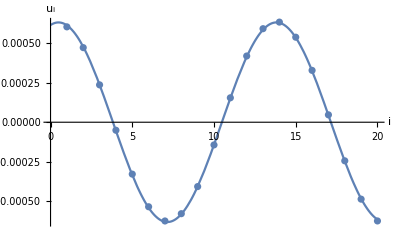

```mathematica
Show[Plot[envTable3[x],{x,0,20},AxesLabel->{"i","u_i"}],ListPlot[harmonicsFreeze[[3]]  ],PlotStyle->Black]
```

## d)

Todos os modos normais

1

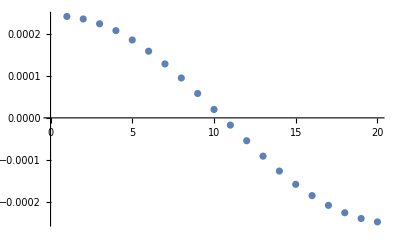

2

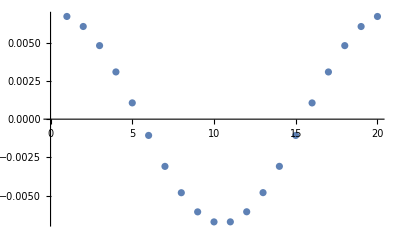

3

-Graphics-

4

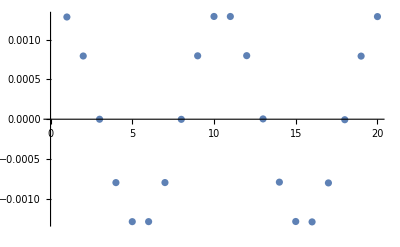

5

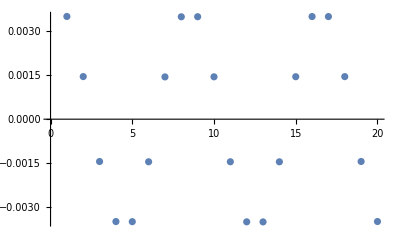

6

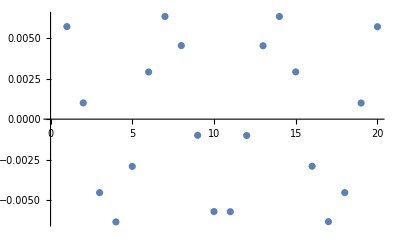

7

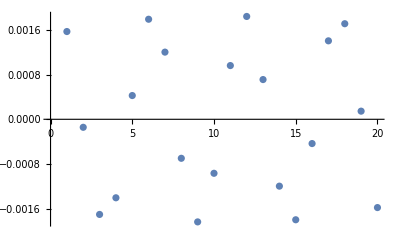

8

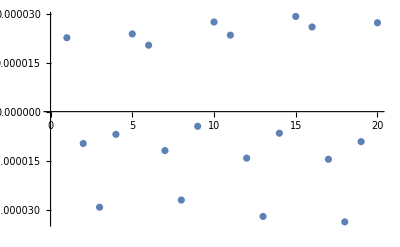

9

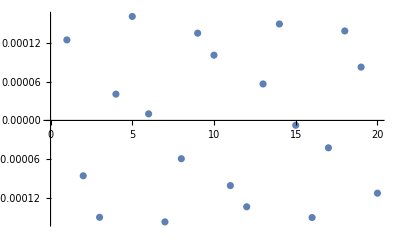

10

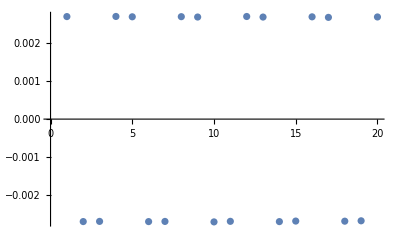

11

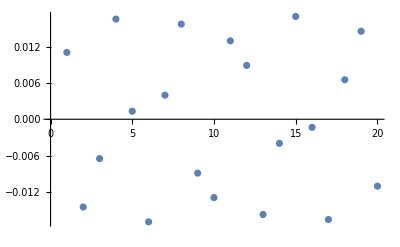

12

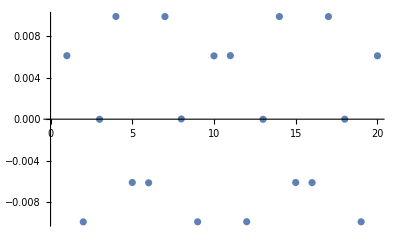

13

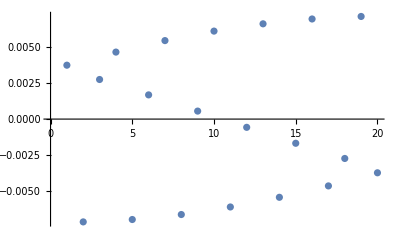

14

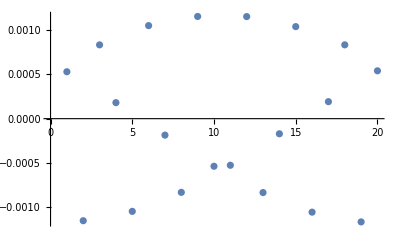

15

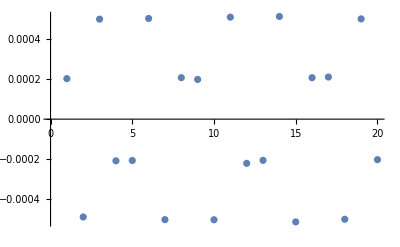

16

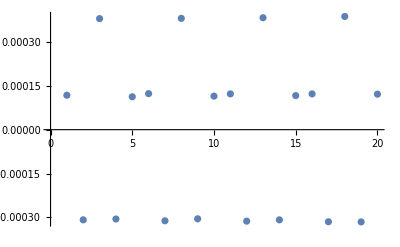

17

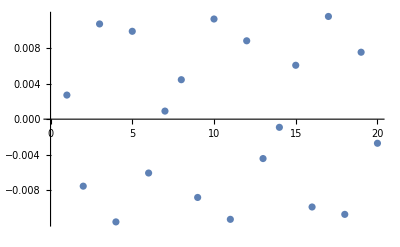

18

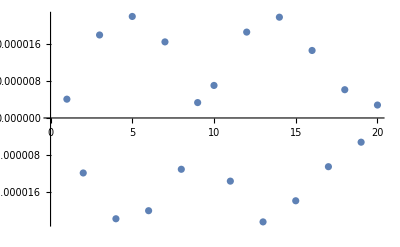

19

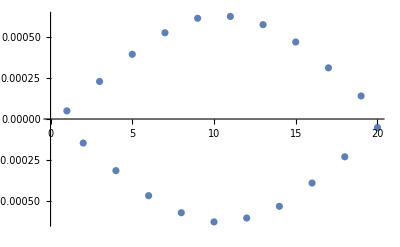

```mathematica
Do[Print[i];Print@ListPlot@harmonicsFreeze[[i]],{i,1,19}]
```

Ajustes para todos modos normais

```mathematica
envTable =Table[NonlinearModelFit[harmonicsFreeze[[i]],A Cos[k x +phi],{{A,Max@harmonicsFreeze[[i]] },{k,2ArcSin[omegaMaxList[[i]] /2]},{phi,0}},x],{i,1,19}]
```

{FittedModel[0.000244526 Cos[0.0686727-0.15578 x]],FittedModel[0.00679452 Cos[0.157111-0.314164 x]],FittedModel[0.000632091 Cos[0.22899-0.471333 x]],FittedModel[0.00135429 Cos[0.312035-0.627968 x]],FittedModel[0.00377188 Cos[0.393833-0.785425 x]],FittedModel[0.00639663 Cos[0.471442-0.942415 x]],FittedModel[0.00184513 Cos[0.552327-1.09963 x]],FittedModel[0.0000309013 Cos[0.532732-1.25711 x]],FittedModel[0.000157266 Cos[0.685921-1.41079 x]],FittedModel[0.00379264 Cos[0.784731-1.57088 x]],FittedModel[0.0170202 Cos[0.863618-1.72786 x]],FittedModel[0.0103895 Cos[0.944166-1.88501 x]],FittedModel[0.00718037 Cos[1.0203-2.04193 x]],FittedModel[0.00117321 Cos[1.09762-2.19941 x]],FittedModel[0.000545322 Cos[1.16451-2.35538 x]],FittedModel[0.000382885 Cos[1.26923-2.51378 x]],FittedModel[0.0115581 Cos[1.33558-2.67038 x]],FittedModel[0.0000210203 Cos[1.63468-2.81836 x]],FittedModel[0.000618052 Cos[1.48177-2.98345 x]]}

1

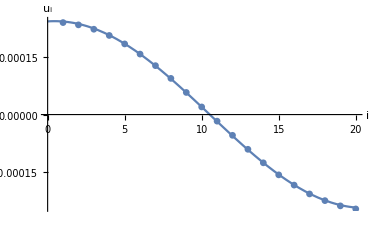

2

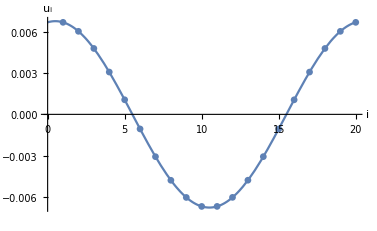

3

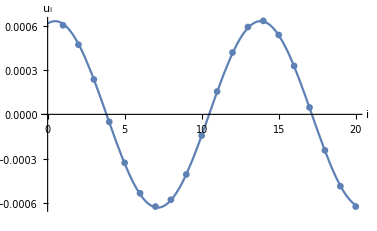

4

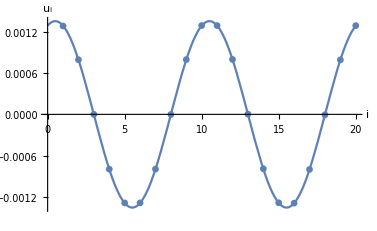

5

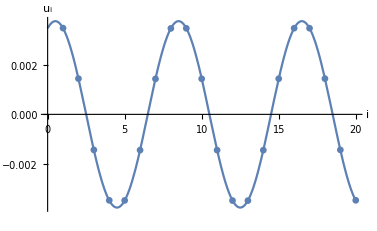

6

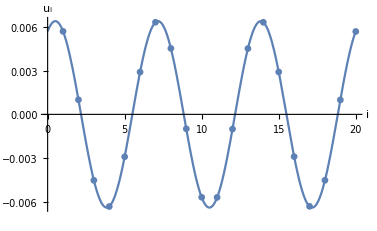

7

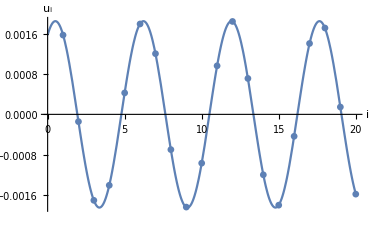

8

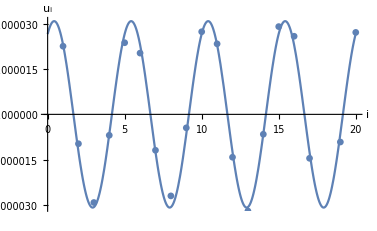

9

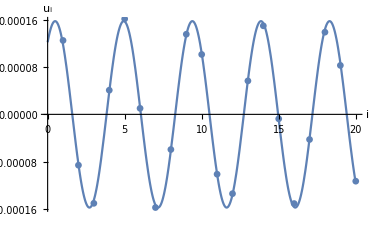

10

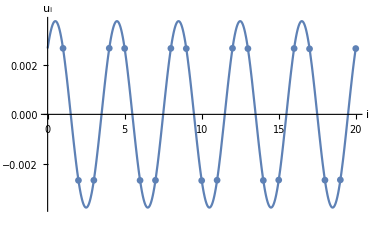

11

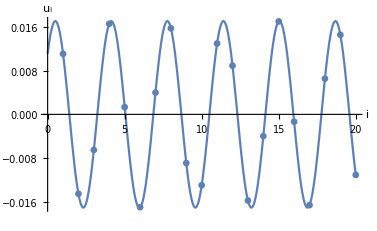

12

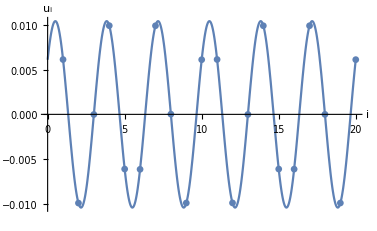

13

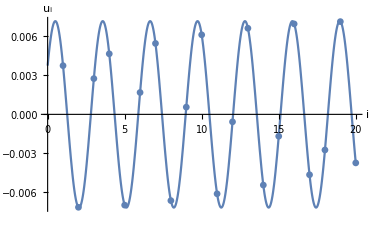

14

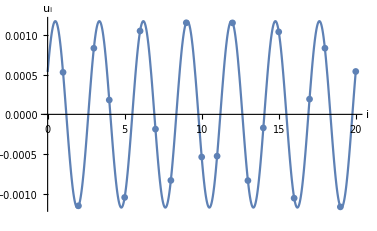

15

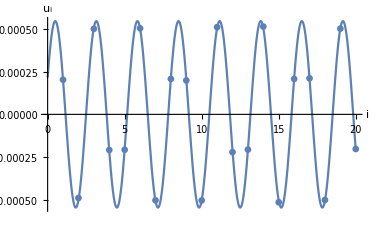

16

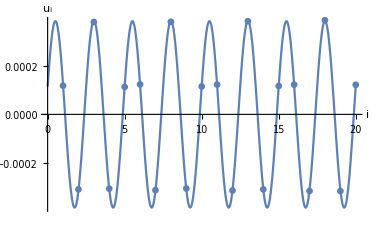

17

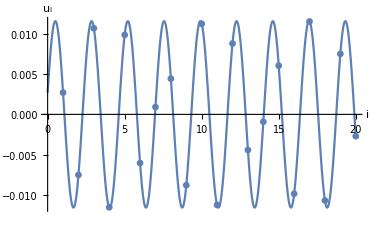

18

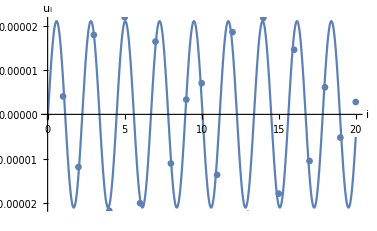

19

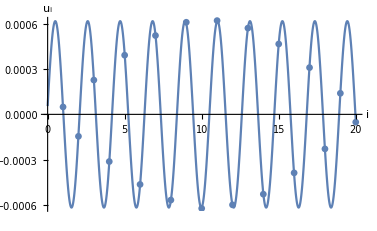

```mathematica
Do[Print[i];Print@Show[Plot[envTable[[i]][x],{x,0,20},AxesLabel->{"i","u_i"}],ListPlot[harmonicsFreeze[[i]]  ],PlotStyle->Black],{i,1,19}]
```

```mathematica
kList=((k/.#["BestFitParameters"])&/@envTable)
```

{0.15578,0.314164,0.471333,0.627968,0.785425,0.942415,1.09963,1.25711,1.41079,1.57088,1.72786,1.88501,2.04193,2.19941,2.35538,2.51378,2.67038,2.81836,2.98345}

Comparação com a relação de dispersão para infinitas massas

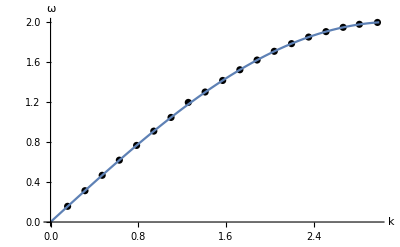

```mathematica
Show[ListPlot[Transpose[{kList,omegaMaxList}][[1;;19]],PlotStyle->Black,AxesLabel->{"k","ω"}],Plot[{2 Sin[k/2]},{k,0,3}]]
```

Transformadas de Fourier Espaciais

```mathematica
split[list_]:= Join[list[[11;;20]],list[[1;;10]] ];
split[Range[-10,9]]
```

{0,1,2,3,4,5,6,7,8,9,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1}

1

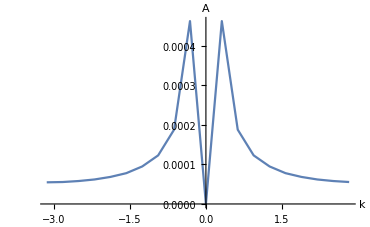

2

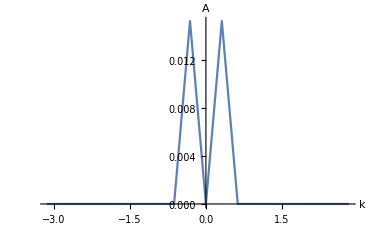

3

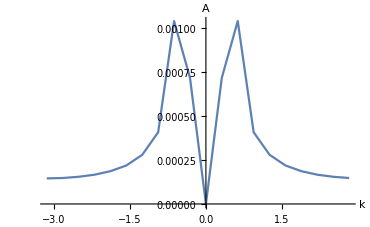

4

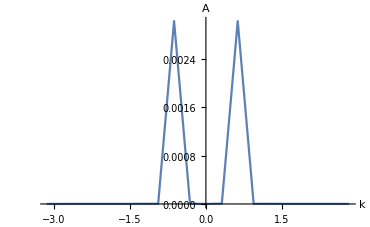

5

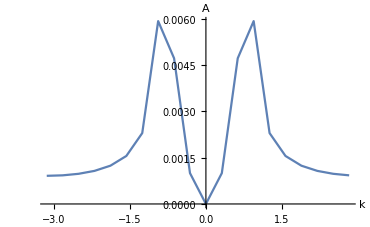

6

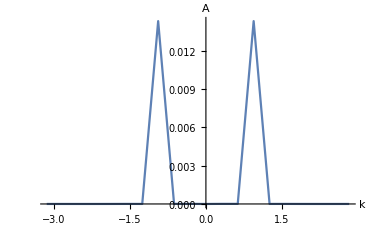

7

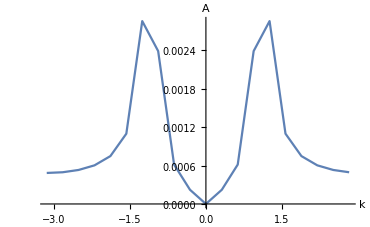

8

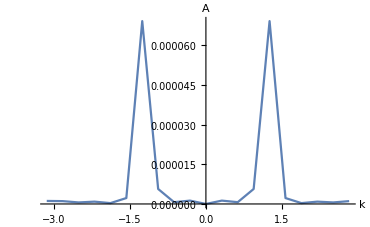

9

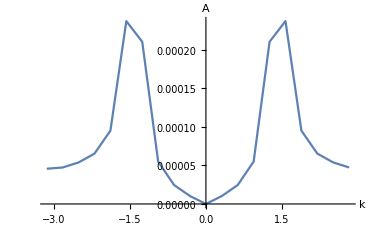

10

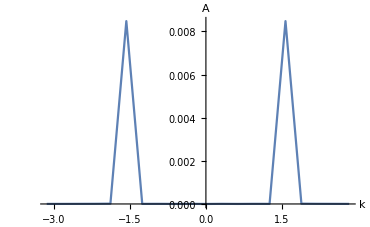

11

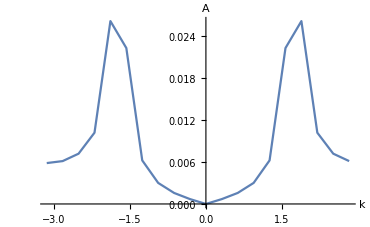

12

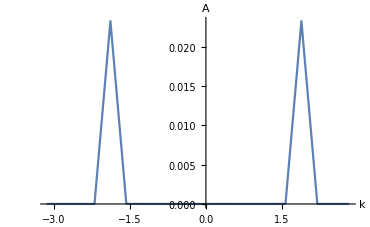

13

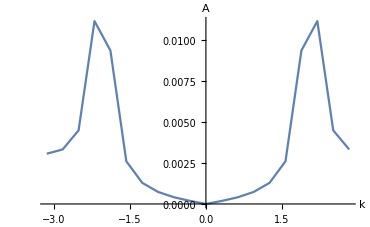

14

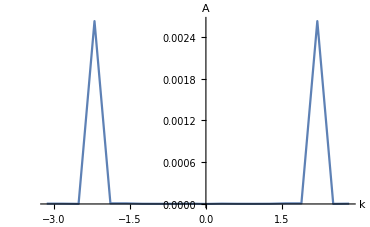

15

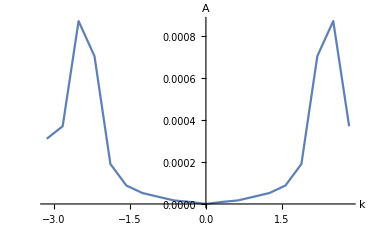

16

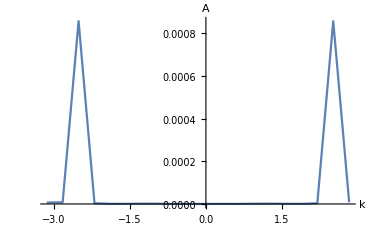

17

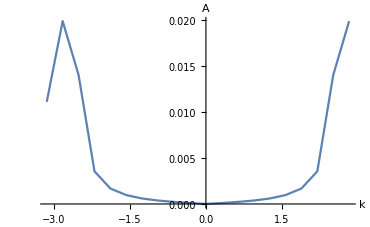

18

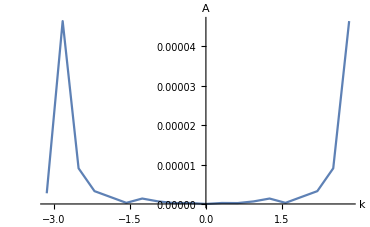

19

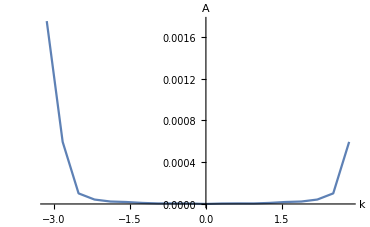

```mathematica
Do[Print[i];Print[ListLinePlot[    Transpose[{2 Pi /20 Range[-10,9],split[Abs@Fourier@harmonicsFreeze[[i]]]}]   ,PlotRange->All,AxesLabel->{"k","A"}]],{i,1,19}]
```

```mathematica
kFFT=Abs/@Fourier/@harmonicsFreeze;
```

```mathematica
kFFT[[3]]
```

{7.67937×10^-16,0.000716134,0.00103745,0.000407019,0.000278894,0.000218295,0.000185918,0.000165994,0.00015418,0.000147204,0.000145122,0.000147204,0.00015418,0.000165994,0.000185918,0.000218295,0.000278894,0.000407019,0.00103745,0.000716134}

```mathematica
kFFTs = Abs/@Fourier/@harmonicsFreeze;
```

Máximo k das transformadas de Fourier Espaciais

```mathematica
maxk=Table[2Pi/20.(First@Ordering[kFFTs[[i,1;;10]],-1]-1),{i,1,19}]
```

{0.314159,0.314159,0.628319,0.628319,0.942478,0.942478,1.25664,1.25664,1.5708,1.5708,1.88496,1.88496,2.19911,2.19911,2.51327,2.51327,2.82743,2.82743,2.82743}